```mathematica
path="Github/peierls/";
darkBlue=RGBColor[0.,0.4,.8]
lightBlue=RGBColor[0.486,0.976,0.949]
```

Github/peierls/

RGBColor[0., 0.4, 0.8]

RGBColor[0.486, 0.976, 0.949]

FittedModel[0.0254084 2.45734^x]

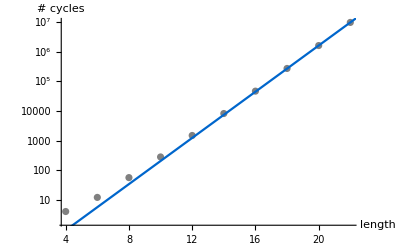

```mathematica
oeis={{2,0},{4,4},{6,12},{8,56},{10,280},{12,1488},{14,8232},{16,47008},{18,274824},{20,1636520},{22,9890584}};
nlm=NonlinearModelFit[oeis,a*b^x,{a,b,c},x]
Show[
ListLogPlot[oeis,PlotStyle->Gray,AxesLabel->{"length","# cycles"}],
LogPlot[nlm[x],{x,0,40},PlotStyle->darkBlue]
]
Export[path<>"expFit.png",%];
```

## 2D

```mathematica
H=7;
g=GridGraph[{H,H},VertexStyle-> lightBlue,VertexSize->0.15,ImageSize->Medium];
```

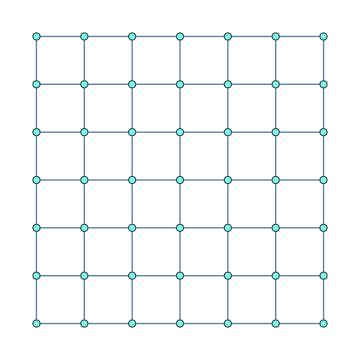

```mathematica
Row[{Show[g],PointLegend[{lightBlue,darkBlue},{"+1","-1"}]}]
```

```mathematica
Export[path<>"Ising2D_Ordered.png",%]
```

Github/peierls/Ising2D_Ordered.png

```mathematica
g2=RandomChoice@FindCycle[{g,18},{16},1000];
p=Polygon[({(#-If[Mod[#,H]==0,H,Mod[#,H]])/H+1,Mod[#,H]/. 0-> H}&/@VertexList[g2])];
vs=(H(#1-1)+#2)&@@@DeleteCases[Tuples[Range[H],2],x_/;!RegionMember[p,x]];
Row[{HighlightGraph[g,Style[Join[vs,g2],darkBlue,Thick]],PointLegend[{lightBlue,darkBlue},{"+1","-1"},LegendMarkerSize->20]}]
```

-Graphics-

```mathematica
Export[path<>"Ising2D_Inverted.png",%]
```

Github/peierls/Ising2D_Inverted.png

```mathematica
rg=DeleteDuplicates@RandomInteger[H^2,40];Row[{HighlightGraph[g,Style[rg,darkBlue]],PointLegend[{lightBlue,darkBlue},{"+1","-1"},LegendMarkerSize->20]}]
```

-Graphics-

```mathematica
Export[path<>"IsingFirstTime.png",%]
```

Github/peierls/IsingFirstTime.png

1D

```mathematica
s1=Range[12];
s2={2,5,8,9};
g1=NearestNeighborGraph[s1,{All,1.},EdgeShapeFunction->"Line",VertexStyle-> lightBlue,VertexSize->0.15,ImageSize->800];
g2=NearestNeighborGraph[s2,{All,1.},EdgeShapeFunction->"Line",VertexStyle->darkBlue,VertexSize->0.15];
```

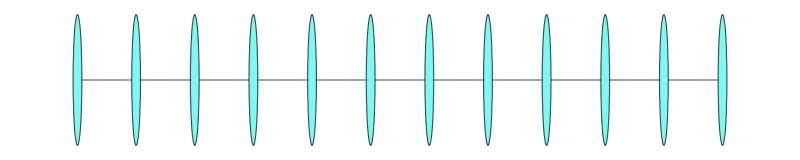

Github/peierls/Ising1D_Ordered.png

/home/gabriel/Dropbox/Blog/Peierls/Ising1D_Ordered.png

```mathematica
Row[{g1,PointLegend[{lightBlue,darkBlue},{"+1","-1"},LegendMarkerSize->15]}]
Export[path<>"Ising1D_Ordered.png",%]
```

```mathematica
p1=Row[{HighlightGraph[g1,Style[g2,darkBlue]],PointLegend[{lightBlue,darkBlue},{"+1","-1"},LegendMarkerSize->15]}]
```

-Graphics-

```mathematica
Export[path<>"Different1D.png",%]
```

Github/peierls/Different1D.png

```mathematica
Row[{HighlightGraph[g1,Style[g2,darkBlue]],PointLegend[{lightBlue,darkBlue},{"+1","-1"},LegendMarkerSize->15]}]
Export[path<>"Ising1D_Inverted.png",%]
```

-Graphics-

Github/peierls/Ising1D_Inverted.png

## Dynamic choice of colors in graph

```mathematica
Clear[r1,r2,r3,b1,b2,b3]
n=20;
s1=Range[n];
s2=Sort[DeleteDuplicates[RandomInteger[n,12]]];
Row[{Column[Slider[Dynamic[#]]&/@{r1,r2,r3}],"   ",Column[Slider[Dynamic[#]]&/@{b1,b2,b3}]}]
Dynamic[{r1,r2,r3,b1,b2,b3}]
myRed=RGBColor[r1,r2,r3];
myBlue=RGBColor[b1,b2,b3];
g1=NearestNeighborGraph[s1,{All,1.},EdgeShapeFunction->"Line",VertexStyle-> myRed,VertexSize->0.15,ImageSize->400];
g2=NearestNeighborGraph[s2,{All,1.},EdgeShapeFunction->"Line",VertexStyle->myBlue,VertexSize->0.15];
Dynamic[Row[{HighlightGraph[g1,Style[g2,myBlue]],PointLegend[{myRed,myBlue},{"+1","-1"},LegendMarkerSize->15]}]]
```

### Some polygons

```mathematica
H=7;
g=GridGraph[{H,H},VertexStyle-> lightBlue,VertexSize->0.15,ImageSize->Medium];
g2=FindCycle[{g,18},{8},All];
p=Function[s,Polygon[({(#-If[Mod[#,H]==0,H,Mod[#,H]])/H+1,Mod[#,H]/. 0-> H}&/@VertexList[g2[[s]]])]];
```

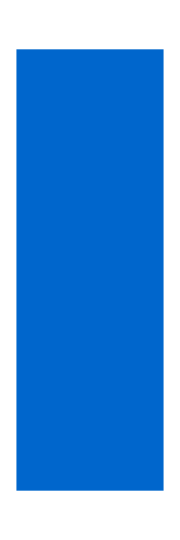
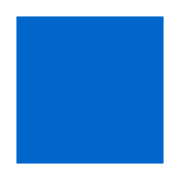
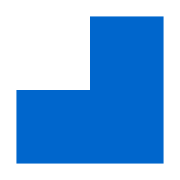
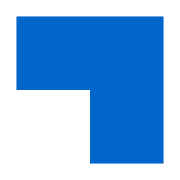
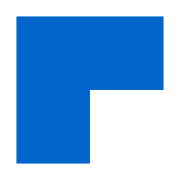
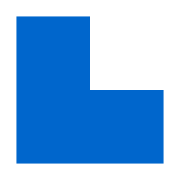
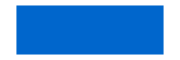

```mathematica
Row[Graphics[{darkBlue,p@#},ImageSize->Small]&/@Range[Length[g2]][[{1,3,4,6,8,9,27}]]]
```

```mathematica
Export[path<>"IsoperimetricPolygons.png",%]
```

Github/peierls/IsoperimetricPolygons.png

## Novel 1D

```mathematica
s1=Range[12];
s2=Range[4,10];
g1=GridGraph[{12},VertexStyle->lightBlue,GraphLayout->{"GridEmbedding","Dimension"-> {1,12}},VertexSize->.15,ImageSize->800];
g2=NearestNeighborGraph[s2,{All,1.},EdgeShapeFunction->"Line",VertexSize->0.15];
```

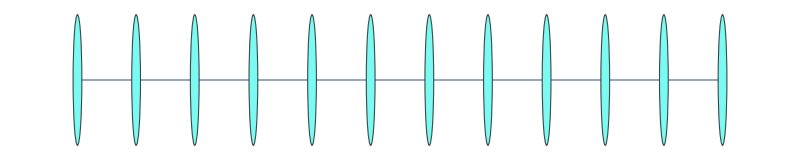

-Graphics-

```mathematica
Row[{g1,PointLegend[{lightBlue,darkBlue},{"+1","-1"},LegendMarkerSize->15]}]
Row[{HighlightGraph[g1,Style[g2,darkBlue]],PointLegend[{lightBlue,darkBlue},{"+1","-1"},LegendMarkerSize->15]}]
```

## Novel 2D

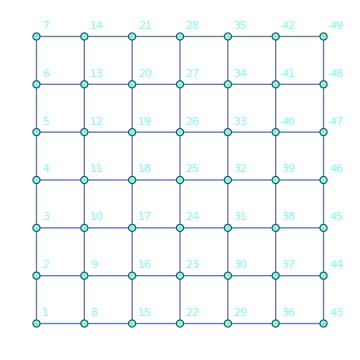

```mathematica
H=7;
g=GridGraph[{H,H},VertexStyle->lightBlue,VertexSize->0.15,ImageSize->Medium,VertexLabels->"Name"]
```

```mathematica
Export[path<>"Ising2D_withLabels.png",%]
```

Github/peierls/Ising2D_withLabels.png

```mathematica
g2=RandomChoice@FindCycle[{g,18},{14},1000];
p=Polygon[({(#-If[Mod[#,H]==0,H,Mod[#,H]])/H+1,Mod[#,H]/.0->H}&/@VertexList[g2])];
vs=(H (#1-1)+#2)&@@@DeleteCases[Tuples[Range[H],2],x_/;!RegionMember[p,x]];
Row[{HighlightGraph[g,Style[Join[vs,g2],darkBlue,Thick]],PointLegend[{lightBlue,darkBlue},{"+1","-1"},LegendMarkerSize->20]}]
```

-Graphics-